```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
a=0.4;
b=0.3;
c={0.5,0.5};
d=0.1;
```

```mathematica
(*check for mu*)
```

```mathematica
tt=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/curvature/discontinuous/solution/dot_e_cur.csv"]
tt=Table[{tt[[i,3]],tt[[i,4]],tt[[i,2]]},{i,2,Length[tt]}]
```

```mathematica
y[t_]:=c+{a Cos[2 π t]/(2+Cos[2 π t]),b Sin[2π t]}
u[y_]:={d y[[1]],-d y[[2]]}
(*this is the current position vector*)
x[t_]:=y[t]+u[y[t]]
ecur[t_]:=x'[t]
ncur[t_]:={x'[t][[2]],-x'[t][[1]]}/Norm[ecur[t]]
```

```mathematica
g[t_]:=ecur[t].ecur[t]
```

```mathematica
bb[t_]:=ecur'[t].ncur[t]
```

```mathematica
H[t_]:=1/(2g[t]) bb[t]
```

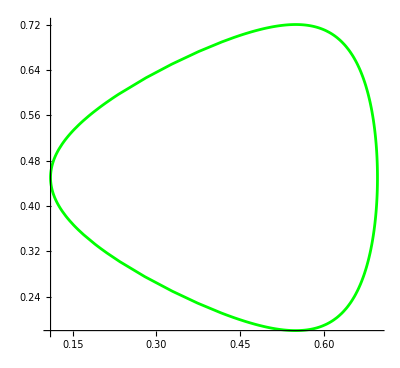

```mathematica
plotX=ParametricPlot[x[t],{t,0,1},PlotStyle->{Green}]
```

```mathematica
(*IMPORTANT: to compare with the numerical solution, here I plot g[t], H[t], ... on to of the REFERENCE curve y[t], not on top of the current one. In fact, in the numerical calculation g, H, .... take the correct values when computed on \partial \Omega^y_circle, not on \partial \Omega_circle*)
```

```mathematica
plotexact=ParametricPlot3D[{y[t][[1]],y[t][[2]],ecur'[t][[2]]},{t,0,1},PlotStyle->{Blue}]
```

-Graphics3D-

```mathematica
plotnum=ListPointPlot3D[tt,PlotRange->Full,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotexact,plotnum,BoxRatios->{1,1,0.5}]
```

-Graphics3D-